```mathematica
a=1;
p=0.1;
n=4;
ConstOriginal[n_,R_]:= (a^n p^n(4π)^n π)/((2π)^2 R 2^n Factorial[n-2])

f3D[n_,R_,ℓ_]:=Binomial[n,ℓ] (-1)^ℓ (a(n-2ℓ)-R)^(n-2)Sign[a(n-2ℓ)-R];

z3D[n_,R_]:=ConstOriginal[n,R] Sum[f3D[n,R,ℓ],{ℓ,0,n}]
z3Dn[n_,R_]:=4 π R^2 z3D[n,R]
```

```mathematica
P[r_]:=r^2 z3D[n,r]/c
```

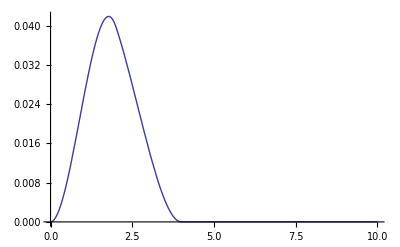

```mathematica
Plot[P[x],{x,0,10}]
```

```mathematica
c=Integrate[z3Dn[n,r],{r,0,n}]
```

2.49367